## Graphics

Elliptic curve [2 Marks]

Use Manipulate and ContourPlot to visualize the elliptic curve y^2==x^3+a x+b over [-3,3]×[-3,3] as a function of the parameters a and b for -3≤a≤3 and -3≤b≤3. [2 Marks]

Solution

Use Manipulate to control a and b: [2 Marks]

```mathematica
Manipulate[
ContourPlot[y^2==x^3+a x+b,{x,-3,3},{y,-3,3},PlotPoints->50],
{{a,1},-3,3},{{b,1},-3,3}]
```

Alternatively, rewrite a x+b=={a,b}.{x,1} and control the point c={a,b} using a Locator, here displaying the coordinates of c:

```mathematica
Manipulate[
ContourPlot[y^2==x^3+c.{x,1},{x,-3,3},{y,-3,3},PlotPoints->50],
{{c,{1,1}},{-3,-3},{3,3},Locator,Appearance->c}]
```

## Programming

Iteration [5 Marks]

Given the vertices of an triangle in the plane,

```mathematica
vertices=N[({{0, 0}, {1, 0}, {0.3, 1}})];
```

displayed using Polygon,

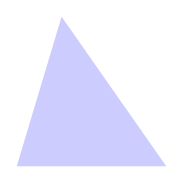

```mathematica
triangle=Graphics[{Blue,Opacity[0.2],Polygon[vertices]},PlotRange->{{0,1},{0,1}},AspectRatio->Automatic]
```

and an arbitrary starting point:

```mathematica
start=RandomReal[{0,1},{2}]
```

{0.498282,0.326802}

consider the following iterative scheme:

At each step, define a function called next[point_]:=... which selects one of the vertices at random (using RandomChoice), and computes the next point in the iterative sequence by taking the midpoint between the current point, point, and the selected vertex. [2 Marks]

Iterate this operation 5 10^4 times from start using NestList. [1 Mark]

Display the sequence of points overlaid onto triangle, using Take and Manipulate to control how many points are displayed. [2 Marks]

Solution

Define next: [2 Marks]

```mathematica
next[point_]:=(RandomChoice[vertices]+point)/2
```

For example,

```mathematica
next[start]
```

{0.749141,0.163401}

Iterate this operation 5 10^4 times using NestList to obtain a sequence of points: [1 Mark]

```mathematica
points=NestList[next,start,50000];
```

Display the sequence of points overlaid onto triangle using Take and Manipulate to control how many points are displayed: [2 Marks]

```mathematica
Manipulate[Show[Graphics[{AbsolutePointSize[0.5],Point[Take[points,i]]}],triangle],{{i,400},1,50000,20},SaveDefinitions->True]
```

## Linear Algebra

Conic sections [5 Marks]

Conic sections have the form of a second-degree polynomial:

a x^2+b x y+c y^2+d x+e y+f==0

A curve passing through five points {x_i,y_i}_(i=1,…5) can be computed by solving the following determinantal equation:

|x^2 | x y | y^2 | x | y | 1
x_1^2 | x_1 y_1 | y_1^2 | x_1 | y_1 | 1
x_2^2 | x_2 y_2 | y_2^2 | x_2 | y_2 | 1
x_3^2 | x_3 y_3 | y_3^2 | x_3 | y_3 | 1
x_4^2 | x_4 y_4 | y_4^2 | x_4 | y_4 | 1
x_5^2 | x_5 y_5 | y_5^2 | x_5 | y_5 | 1|==0

Use the determinantal equation (DisplayFormulaNumbered) to compute the equation of the curve passing through 5 randomly chosen points, computed using RandomReal. [3 Marks]

Use ContourPlot to visualize the curve. Show the curve together with the points. [2 Marks]

Solution

Each row of the matrix can be constucted from a point {x,y} using a function:

```mathematica
makeRow[{x_,y_}]:={x^2,x y,y^2,x,y,1}
```

Compute the equation of the curve by constructing the matrix and computing the determinant:

```mathematica
conic[x_,y_][pts_]:=Det[makeRow/@Join[{{x,y}},pts]]
```

Check that it works on a random set of points:

```mathematica
pts=RandomReal[{-1,1},{5,2}]
```

(-0.622088 | -0.057854
0.945733 | -0.454633
0.40561 | -0.529854
0.373552 | 0.627669
0.131531 | -0.55893)

```mathematica
conic[x,y][pts]
```

0.0102745 x^2-0.0598044 x y-0.0282633 x+0.0835087 y^2+0.0144882 y-0.0188473

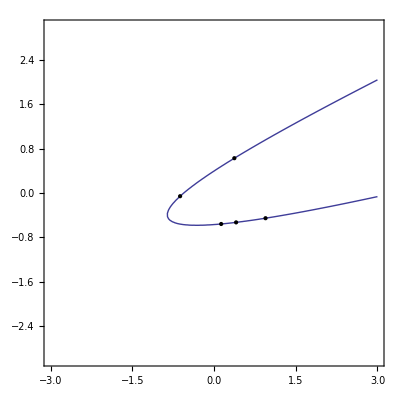

```mathematica
Show[ContourPlot[%==0,{x,-3,3},{y,-3,3},PlotPoints->50],Graphics[Point[pts]]]
```

Make this dynamic:

```mathematica
Manipulate[
ContourPlot[conic[x,y][r]==0,{x,-3,3},{y,-3,3},PlotPoints->50],
{{r,RandomReal[{-1,1},{5,2}]},{-3,-3},{3,3},Locator},SaveDefinitions-> True]
```

Hermitian matrices [7 Marks]

Consider the general 3×3 Hermitian traceless matrix

```mathematica
ℋ=({{α, β+ⅈ γ, δ+ⅈ ϵ}, {β-ⅈ γ, ϕ, η+ⅈ κ}, {δ-ⅈ ϵ, η-ⅈ κ, -α-ϕ}});
```

where all the parameters α,β,…,κ are real.

How many parameters are there in this matrix? [1 Mark]

Verify that ℋ is Hermitian and has zero trace (Hint: use ConjugateTranspose, ComplexExpand, and Tr). [2 Marks]

Show that the set of matrices

```mathematica
X/:Subscript[X, 1]=({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});X/:Subscript[X, 2]=({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 0}});X/:Subscript[X, 3]=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});X/:Subscript[X, 4]=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});X/:Subscript[X, 5]=({{0, 0, -ⅈ}, {0, 0, 0}, {ⅈ, 0, 0}});X/:Subscript[X, 6]=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});X/:Subscript[X, 7]=({{0, 0, 0}, {0, 0, -ⅈ}, {0, ⅈ, 0}});X/:Subscript[X, 8]=({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}});
```

form a basis for 3×3 Hermitian traceless matrices (Hint: this means that ℋ can be written as a linear combination of the Χ_i). [2 Marks]

The commutator of two matrices (or operators) is denoted

[A,B]==A.B-B.A

Show that each commutator [X_a,X_b] can be expressed as a linear combination of X_c. [2 Marks]

Solution

There are 8 free parameters: [1 Mark]

```mathematica
Variables[ℋ]
```

{α,β,γ,δ,ϵ,η,κ,ϕ}

```mathematica
Length[%]
```

8

Verify that ℋ is Hermitian: [1 Mark]

```mathematica
ComplexExpand[ConjugateTranspose[ℋ]==ℋ]
```

True

Verify that ℋ has zero trace: [1 Mark]

```mathematica
Tr[ℋ]
```

0

Show that ℋ can be written as a linear combination of the Χ_i: [2 Marks]

```mathematica
Solve[ℋ==∑_(i=1)^8 Subscript[c, i] Subscript[X, i],Table[Subscript[c, i],{i,8}]]
```

{{c_1→β,c_2→-γ,c_3→(α-ϕ)/2,c_4→δ,c_5→-ϵ,c_6→η,c_7→-κ,c_8→α/2+ϕ/2}}

```mathematica
∑_(i=1)^8 Subscript[c, i] Subscript[X, i]/.First[%]//Simplify
```

(α | β+ⅈ γ | δ+ⅈ ϵ
β-ⅈ γ | ϕ | η+ⅈ κ
δ-ⅈ ϵ | η-ⅈ κ | -α-ϕ)

```mathematica
%==ℋ
```

True

Show that the commutator [X_a,X_b] can be expressed as a linear combination of X_c:

```mathematica
𝒯=Table[Subscript[f, c],{c,8}]/.Table[First@Solve[Subscript[X, a].Subscript[X, b]-Subscript[X, b].Subscript[X, a]== ∑_(c=1)^8 Subscript[f, c] Subscript[X, c],Table[Subscript[f, c],{c,8}]],{a,8},{b,8}]
```

({0,0,0,0,0,0,0,0} | {0,0,2 ⅈ,0,0,0,0,0} | {0,-2 ⅈ,0,0,0,0,0,0} | {0,0,0,0,0,0,ⅈ,0} | {0,0,0,0,0,-ⅈ,0,0} | {0,0,0,0,ⅈ,0,0,0} | {0,0,0,-ⅈ,0,0,0,0} | {0,0,0,0,0,0,0,0}
{0,0,-2 ⅈ,0,0,0,0,0} | {0,0,0,0,0,0,0,0} | {2 ⅈ,0,0,0,0,0,0,0} | {0,0,0,0,0,ⅈ,0,0} | {0,0,0,0,0,0,ⅈ,0} | {0,0,0,-ⅈ,0,0,0,0} | {0,0,0,0,-ⅈ,0,0,0} | {0,0,0,0,0,0,0,0}
{0,2 ⅈ,0,0,0,0,0,0} | {-2 ⅈ,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0} | {0,0,0,0,ⅈ,0,0,0} | {0,0,0,-ⅈ,0,0,0,0} | {0,0,0,0,0,0,-ⅈ,0} | {0,0,0,0,0,ⅈ,0,0} | {0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,-ⅈ,0} | {0,0,0,0,0,-ⅈ,0,0} | {0,0,0,0,-ⅈ,0,0,0} | {0,0,0,0,0,0,0,0} | {0,0,ⅈ,0,0,0,0,ⅈ} | {0,ⅈ,0,0,0,0,0,0} | {ⅈ,0,0,0,0,0,0,0} | {0,0,0,0,-3 ⅈ,0,0,0}
{0,0,0,0,0,ⅈ,0,0} | {0,0,0,0,0,0,-ⅈ,0} | {0,0,0,ⅈ,0,0,0,0} | {0,0,-ⅈ,0,0,0,0,-ⅈ} | {0,0,0,0,0,0,0,0} | {-ⅈ,0,0,0,0,0,0,0} | {0,ⅈ,0,0,0,0,0,0} | {0,0,0,3 ⅈ,0,0,0,0}
{0,0,0,0,-ⅈ,0,0,0} | {0,0,0,ⅈ,0,0,0,0} | {0,0,0,0,0,0,ⅈ,0} | {0,-ⅈ,0,0,0,0,0,0} | {ⅈ,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0} | {0,0,-ⅈ,0,0,0,0,ⅈ} | {0,0,0,0,0,0,-3 ⅈ,0}
{0,0,0,ⅈ,0,0,0,0} | {0,0,0,0,ⅈ,0,0,0} | {0,0,0,0,0,-ⅈ,0,0} | {-ⅈ,0,0,0,0,0,0,0} | {0,-ⅈ,0,0,0,0,0,0} | {0,0,ⅈ,0,0,0,0,-ⅈ} | {0,0,0,0,0,0,0,0} | {0,0,0,0,0,3 ⅈ,0,0}
{0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0} | {0,0,0,0,3 ⅈ,0,0,0} | {0,0,0,-3 ⅈ,0,0,0,0} | {0,0,0,0,0,0,3 ⅈ,0} | {0,0,0,0,0,-3 ⅈ,0,0} | {0,0,0,0,0,0,0,0})

```mathematica
MatrixForm/@𝒯
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3 ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 ⅈ | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -3 ⅈ | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 ⅈ | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 ⅈ | 0 | 0 | 0
0 | 0 | 0 | -3 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 ⅈ | 0
0 | 0 | 0 | 0 | 0 | -3 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

## Calculus

Nonlinear differential equation [3 Marks]

Consider the nonlinear differential equation

w''(z)==2(w(z))^3+z w(z)

with initial conditions

w(0)==a
w'(0)==b

Use NDSolve to compute numerical solutions to (DisplayFormulaNumbered) over -10≤z≤3. [1 Mark]

Use Manipulate to plot w(z) as a function of a and b for 0≤a≤0.5 and -0.2≤b≤0 and compare with 1/2 z. [2 Marks]

Solution

Use NDSolve to compute numerical solutions to the nonlinear differential equation over -10≤z≤3: [1 Mark]

```mathematica
nsol[a_,b_]:=NDSolve[{w''(z)==2(w(z))^3+z w(z),w(0)==a,w'(0)==b},w,{z,-10,3}]
```

Plot w(z) and compare with 1/2 z: [2 Marks]

```mathematica
Manipulate[Plot[Evaluate[{w(z)/.nsol[a,b],1/2 z}],{z,-10,3},PlotRange->1/2],{{a,0.18},0,0.5},{{b,-0.13},-0.2,0},SaveDefinitions->True]
```

w(z) and 1/2 z are similar, with a small phase difference. Suitable choices of a and b can make them agree for z>0.

Functional equation [3 Marks]

Consider the functional equation

f(z)=α f(f(z /α)).

One method for computing the value of α for which f(z) exists is to assume that

f_n(z)=1+∑_(k=1)^n c_k z^(2k),

and compute successive approximations to α for n=1,2,3,…, using series expansion of (both sides) of equation (DisplayFormulaNumbered).

Use series expansion and Solve to compute approximate values of α<0 and c_1<0 for n=1. These approximate values can be obtained exactly. [2 Marks]

Use series expansion and NSolve to compute approximate values of α<0, c_1<0, and c_2 for n=2. [1 Mark]

Solution

Use series expansion and Solve to compute approximate values of α<0 and c_1<0:

```mathematica
Subscript[f, n_](z_):=1+∑_(k=1)^n Subscript[c, k] z^(2k)
```

```mathematica
Solve[(f(z)-α f(f(z /α))/.f->Subscript[f, 1])+O[z]^3==0∧Subscript[c, 1]<0,{α,Subscript[c, 1]}]
```

{{α→-1-√3,c_1→1/2 (-1-√3)}}

```mathematica
N[%]
```

{{α→-2.73205,c_1→-1.36603}}

Use series expansion and NSolve to compute approximate values for n=2:

```mathematica
NSolve[(f(z)-α f(f(z /α))/.f->Subscript[f, 2])+O[z]^5==0∧α<0∧Subscript[c, 1]<0,{α,Subscript[c, 1],Subscript[c, 2]}]
```

{{α→-2.53403,c_1→-1.52224,c_2→0.127613}}

## Variational Methods

Coulomb potential inside heavy neutral atoms [7 Marks]

The nonlinear differential equation

ϕ''(x)==(ϕ(x))^(3/2)/(√x),

along with the boundary conditions

ϕ(0)==1,ϕ(∞)==0,

describes the screening of the Coulomb potential inside heavy neutral atoms. However, there is no closed-form solution of equation (DisplayFormulaNumbered).

The Euler–Lagrange equation

(∂ℱ)/(∂ϕ)-ⅆ_x(∂ℱ)/(∂ϕ')==0

applied to the functional

ℱ[ϕ][x]==1/2(ϕ'(x))^2+2/5(ϕ(x))^(5/2)/(√x)

yields the differential equation (DisplayFormulaNumbered).

Show that ϕ_0(x)==144 x^-3 satisfies the differential equation (DisplayFormulaNumbered) for x≥0 and the second boundary condition ϕ(∞)==0. [2 Marks]

Show that the Euler–Lagrange equation (DisplayFormulaNumbered) applied to functional (DisplayFormulaNumbered) yields the differential equation (DisplayFormulaNumbered). [2 Marks]

Consider the two-parameter trial function

ϕ_(α,β)(x)=1/((1+(x/β)^(3/α))^α)

Given that

⟨ℱ_(α,β)⟩=∫_0^∞ ℱ[ϕ_(α,β)][x]==(4 √β α/6+1 (7 α)/3)/(5 (5 α)/2)+(9 2-α/3 (7 α)/3+1)/(14 β 2 α+2)

use FindRoot to obtain the optimal values of α>0 and β>0 by determining the stationary value of ⟨ℱ_(α,β)⟩, and plot the resulting variational solution ϕ_(α,β)(x). [3 Marks]

Solution

Define ϕ_0(x):

```mathematica
Subscript[ϕ, 0](x_)=144/x^3;
```

It satisfies the differential equation (DisplayFormulaNumbered) for x≥0: [1 Mark]

```mathematica
Simplify[ϕ''(x)==(ϕ(x))^(3/2)/(√x)/.ϕ->Subscript[ϕ, 0],x≥0]
```

True

It satisfies the second boundary condition ϕ(∞)==0: [1 Mark]

```mathematica
lim_(x->∞) Subscript[ϕ, 0](x)
```

0

Define the functional (DisplayFormulaNumbered): [1 Mark]

```mathematica
ℱ[ϕ_][x_]:=1/2(ϕ'(x))^2+2/5(ϕ(x))^(5/2)/(√x)
```

Show that the Euler–Lagrange equation (DisplayFormulaNumbered) applied to functional (DisplayFormulaNumbered) yields the differential equation (DisplayFormulaNumbered):  [1 Mark]

```mathematica
(∂ℱ[ϕ][x])/(∂ϕ(x))-Subscript[ⅆ, x](∂ℱ[ϕ][x])/(∂ϕ'(x))==0//Simplify
```

ϕ''(x)==(ϕ(x))^(3/2)/(√x)

Define the two-parameter trial function and ⟨ℱ_(α,β)⟩: [1 Mark]

```mathematica
Subscript[ϕ, α_,β_](x_)=1/((1+(x/β)^(3/α))^α);
```

```mathematica
⟨Subscript[ℱ, α_,β_]⟩=(4 √β α/6+1 (7 α)/3)/(5 (5 α)/2)+(9 2-α/3 (7 α)/3+1)/(14 β 2 α+2);
```

Use FindRoot to obtain the optimal values of α>0 and β>0 by determining the stationary value of ⟨ℱ_(α,β)⟩: [1 Mark]

```mathematica
FindRoot[{(∂⟨Subscript[ℱ, α,β]⟩)/(∂α)==0,(∂⟨Subscript[ℱ, α,β]⟩)/(∂β)==0},{α,5},{β,3}]
```

{α→3.36169,β→3.96707}

Plot the resulting variational solution ϕ_(α,β)(x). [1 Mark]

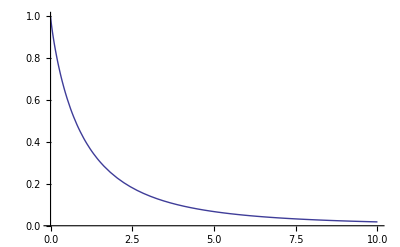

```mathematica
Plot[Evaluate[Subscript[ϕ, α,β](x)/.%],{x,0,10},PlotRange->All]
```

## Fourier Series

Fourier Transform [8 Marks]

The Fourier transform of a function f(t) is defined to be

f̃(ω)==1/(2π)∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω t)ⅆt

The inverse Fourier transform of a function f̃(ω) is defined to be

f(t)==∫_(-∞)^∞ f̃(ω)ⅇ^(-ⅈ ω t)ⅆω

Consider the function

s(t)=Piecewise[{{1, -1<t<1}, {0, Abs[t]≥1}}]

Compute the Fourier transform s̃(ω) of s(t) and plot it for -12≤ω≤12. [2 Marks]

Compute the complex Fourier coefficients c_n of s(t) for t∈[-π,π], with s(t) periodically extended outside this interval. [2 Marks]

Use DiscretePlot to visualize c_n for -12≤n≤12. [1 Mark]

Verify that c_n==s̃(n). [1 Mark]

Compute the inverse Fourier transform of s̃(ω) and verify that you recover s(t). [2 Marks]

Solution

Define s(t):

```mathematica
s(t_):=Piecewise[{{1, -1<t<1}, {0, Abs[t]≥1}}]
```

Compute the Fourier Transform of s(t):

```mathematica
s̃(ω_)=1/(2π)∫_(-∞)^∞ s(t)ⅇ^(ⅈ ω t)ⅆt
```

(sin(ω))/(π ω)

Plot s̃(ω) for -12≤ω≤12:

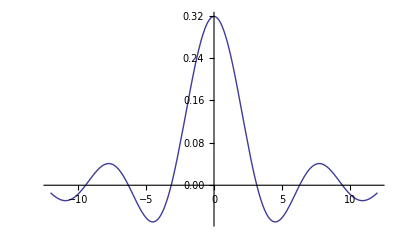

```mathematica
plot=Plot[s̃(ω),{ω,-12,12}]
```

Compute the complex Fourier coefficients c_n:

```mathematica
c/:Subscript[c, 0]=Simplify[1/(2π)∫_-π^π s(t) ⅆt,n∈ℤ]
```

1/π

```mathematica
c/:Subscript[c, n_]=Simplify[1/(2π)∫_-π^π s(t) ⅇ^(ⅈ n t)ⅆt,n∈ℤ]
```

(sin(n))/(π n)

Use DiscretePlot to visualize c_n for -12≤n≤12:

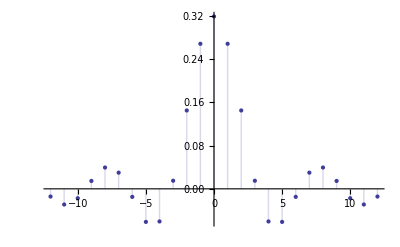

```mathematica
cplot=DiscretePlot[Subscript[c, n],{n,-12,12}]
```

Verify that c_n==s̃(n):

```mathematica
Subscript[c, n]==s̃(n)
```

True

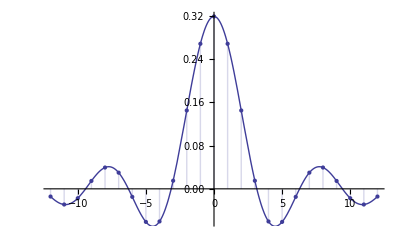

```mathematica
Show[cplot,plot]
```

Compute the inverse Fourier transform of s̃(ω) to recover s(t), considering the two cases 0<t<1 and Abs[t]>1 separately:

```mathematica
Assuming[0<t<1,∫_(-∞)^∞ s̃(ω)ⅇ^(-ⅈ ω t)ⅆω]
```

1

```mathematica
Assuming[Abs[t]>1,∫_(-∞)^∞ ⅇ^(-ⅈ t ω) s̃(ω)ⅆω]
```

0

## Special Functions

Roots of the Airy function [9 Marks]

The Airy function Ai(z) can be written as an infinite product over its roots,

Ai(z)==Ai(0)ⅇ^(z 0/0)∏_(n=1)^∞ (1-z/a_n)ⅇ^(z/a_n)

where a_n is the n^th zero of Ai(z). The logarithmic derivative of Ai(z) reads

(Ai'(z))/(Ai(z))==0/0-∑_(k=1)^∞ z^k Z(k+1)

where

Z(k)==∑_(n=1)^∞ 1/a_n^k

Plot z over -15≤z≤5. What do you observe about the location and spacing of the roots of z? [2 Marks]

The zeros of the z are built-in as AiryAiZero. Use N to compute numerical values of the first 1000 roots. [1 Mark]

Compute Z(2), Z(3), and Z(4) exactly by computing the Maclaurin series expansion of equation (DisplayFormulaNumbered). [2 Marks]

Show that Z(2), Z(3), and Z(4) are polynomials in r=0/0. [2 Marks]

Compare Z(2), Z(3), and Z(4) with the numerical value of the truncated sum (DisplayFormulaNumbered), computed using the numerical roots. [2 Marks]

Solution

Plot z over -15≤z≤5:

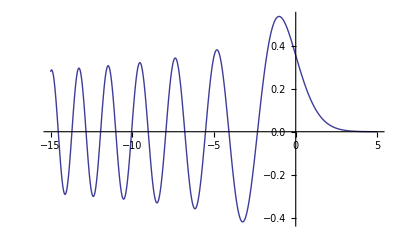

```mathematica
Plot[z,{z,-15,5}]
```

All the roots are negative and are getting closer together as z→-∞.

Compute numerical values of the first 1000 roots of z:

```mathematica
zeros=Table[AiryAiZero[n]//N,{n,1000}]
```

{-2.33811,-4.08795,-5.52056,-6.78671,-7.94413,-9.02265,-10.0402,-11.0085,-11.936,-12.8288,-13.6915,-14.5278,-15.3408,-16.1327,-16.9056,-17.6613,-18.4011,-19.1264,-19.8381,-20.5373,-21.2248,-21.9014,-22.5676,-23.2242,-23.8716,-24.5103,-25.1408,-25.7635,-26.3788,-26.987,-27.5884,-28.1833,-28.772,-29.3548,-29.9318,-30.5033,-31.0695,-31.6306,-32.1867,-32.7381,-33.2849,-33.8272,-34.3652,-34.8991,-35.4289,-35.9547,-36.4767,-36.9951,-37.5098,-38.021,-38.5288,-39.0333,-39.5345,-40.0326,-40.5276,-41.0196,-41.5087,-41.9948,-42.4782,-42.9589,-43.4369,-43.9123,-44.3851,-44.8554,-45.3233,-45.7887,-46.2518,-46.7126,-47.1711,-47.6274,-48.0816,-48.5336,-48.9835,-49.4314,-49.8772,-50.321,-50.7629,-51.2029,-51.641,-52.0773,-52.5117,-52.9443,-53.3752,-53.8044,-54.2318,-54.6576,-55.0817,-55.5042,-55.9251,-56.3444,-56.7621,-57.1784,-57.5931,-58.0063,-58.4181,-58.8284,-59.2373,-59.6447,-60.0508,-60.4556,-60.8589,-61.261,-61.6617,-62.0611,-62.4593,-62.8562,-63.2518,-63.6462,-64.0394,-64.4314,-64.8221,-65.2118,-65.6002,-65.9875,-66.3737,-66.7588,-67.1427,-67.5256,-67.9073,-68.288,-68.6677,-69.0463,-69.4238,-69.8004,-70.1759,-70.5504,-70.9239,-71.2965,-71.6681,-72.0387,-72.4084,-72.7771,-73.1449,-73.5117,-73.8777,-74.2428,-74.6069,-74.9702,-75.3326,-75.6941,-76.0548,-76.4146,-76.7735,-77.1317,-77.489,-77.8454,-78.2011,-78.556,-78.91,-79.2633,-79.6158,-79.9675,-80.3184,-80.6686,-81.018,-81.3666,-81.7145,-82.0617,-82.4081,-82.7538,-83.0988,-83.4431,-83.7867,-84.1295,-84.4717,-84.8131,-85.1539,-85.494,-85.8335,-86.1722,-86.5103,-86.8478,-87.1845,-87.5207,-87.8562,-88.191,-88.5252,-88.8588,-89.1918,-89.5241,-89.8558,-90.187,-90.5175,-90.8474,-91.1767,-91.5054,-91.8335,-92.1611,-92.488,-92.8144,-93.1402,-93.4654,-93.7901,-94.1142,-94.4378,-94.7608,-95.0832,-95.4051,-95.7265,-96.0473,-96.3676,-96.6874,-97.0066,-97.3253,-97.6435,-97.9612,-98.2783,-98.595,-98.9111,-99.2268,-99.5419,-99.8565,-100.171,-100.484,-100.797,-101.11,-101.422,-101.734,-102.045,-102.356,-102.666,-102.976,-103.285,-103.594,-103.903,-104.211,-104.518,-104.825,-105.132,-105.438,-105.744,-106.049,-106.354,-106.658,-106.962,-107.266,-107.569,-107.872,-108.174,-108.476,-108.777,-109.078,-109.379,-109.679,-109.979,-110.278,-110.577,-110.876,-111.174,-111.472,-111.769,-112.066,-112.363,-112.659,-112.955,-113.25,-113.545,-113.84,-114.134,-114.428,-114.721,-115.014,-115.307,-115.599,-115.891,-116.183,-116.474,-116.765,-117.056,-117.346,-117.636,-117.925,-118.214,-118.503,-118.792,-119.08,-119.367,-119.655,-119.942,-120.229,-120.515,-120.801,-121.087,-121.372,-121.657,-121.942,-122.226,-122.51,-122.794,-123.077,-123.36,-123.643,-123.925,-124.207,-124.489,-124.77,-125.051,-125.332,-125.612,-125.893,-126.172,-126.452,-126.731,-127.01,-127.289,-127.567,-127.845,-128.123,-128.4,-128.677,-128.954,-129.231,-129.507,-129.783,-130.058,-130.334,-130.609,-130.883,-131.158,-131.432,-131.706,-131.979,-132.253,-132.526,-132.799,-133.071,-133.343,-133.615,-133.887,-134.158,-134.429,-134.7,-134.971,-135.241,-135.511,-135.781,-136.05,-136.319,-136.588,-136.857,-137.125,-137.394,-137.661,-137.929,-138.196,-138.464,-138.73,-138.997,-139.263,-139.529,-139.795,-140.061,-140.326,-140.591,-140.856,-141.121,-141.385,-141.649,-141.913,-142.177,-142.44,-142.703,-142.966,-143.228,-143.491,-143.753,-144.015,-144.277,-144.538,-144.799,-145.06,-145.321,-145.581,-145.842,-146.102,-146.361,-146.621,-146.88,-147.139,-147.398,-147.657,-147.915,-148.174,-148.432,-148.689,-148.947,-149.204,-149.461,-149.718,-149.975,-150.231,-150.487,-150.743,-150.999,-151.255,-151.51,-151.765,-152.02,-152.275,-152.529,-152.783,-153.038,-153.291,-153.545,-153.798,-154.052,-154.305,-154.557,-154.81,-155.062,-155.315,-155.567,-155.818,-156.07,-156.321,-156.573,-156.824,-157.074,-157.325,-157.575,-157.825,-158.075,-158.325,-158.575,-158.824,-159.073,-159.322,-159.571,-159.82,-160.068,-160.316,-160.564,-160.812,-161.06,-161.307,-161.554,-161.802,-162.048,-162.295,-162.542,-162.788,-163.034,-163.28,-163.526,-163.771,-164.017,-164.262,-164.507,-164.752,-164.997,-165.241,-165.485,-165.729,-165.973,-166.217,-166.461,-166.704,-166.947,-167.19,-167.433,-167.676,-167.919,-168.161,-168.403,-168.645,-168.887,-169.129,-169.37,-169.611,-169.853,-170.093,-170.334,-170.575,-170.815,-171.056,-171.296,-171.536,-171.776,-172.015,-172.255,-172.494,-172.733,-172.972,-173.211,-173.449,-173.688,-173.926,-174.164,-174.402,-174.64,-174.878,-175.115,-175.352,-175.59,-175.827,-176.063,-176.3,-176.537,-176.773,-177.009,-177.245,-177.481,-177.717,-177.953,-178.188,-178.423,-178.658,-178.893,-179.128,-179.363,-179.597,-179.832,-180.066,-180.3,-180.534,-180.767,-181.001,-181.234,-181.468,-181.701,-181.934,-182.167,-182.399,-182.632,-182.864,-183.097,-183.329,-183.561,-183.792,-184.024,-184.256,-184.487,-184.718,-184.949,-185.18,-185.411,-185.642,-185.872,-186.103,-186.333,-186.563,-186.793,-187.023,-187.252,-187.482,-187.711,-187.94,-188.169,-188.398,-188.627,-188.856,-189.084,-189.313,-189.541,-189.769,-189.997,-190.225,-190.453,-190.68,-190.908,-191.135,-191.362,-191.589,-191.816,-192.043,-192.27,-192.496,-192.722,-192.949,-193.175,-193.401,-193.627,-193.852,-194.078,-194.303,-194.529,-194.754,-194.979,-195.204,-195.429,-195.653,-195.878,-196.102,-196.326,-196.551,-196.775,-196.998,-197.222,-197.446,-197.669,-197.893,-198.116,-198.339,-198.562,-198.785,-199.008,-199.23,-199.453,-199.675,-199.898,-200.12,-200.342,-200.564,-200.785,-201.007,-201.229,-201.45,-201.671,-201.892,-202.113,-202.334,-202.555,-202.776,-202.996,-203.217,-203.437,-203.657,-203.877,-204.097,-204.317,-204.537,-204.757,-204.976,-205.195,-205.415,-205.634,-205.853,-206.072,-206.291,-206.509,-206.728,-206.946,-207.165,-207.383,-207.601,-207.819,-208.037,-208.255,-208.472,-208.69,-208.907,-209.124,-209.342,-209.559,-209.776,-209.992,-210.209,-210.426,-210.642,-210.859,-211.075,-211.291,-211.507,-211.723,-211.939,-212.155,-212.37,-212.586,-212.801,-213.017,-213.232,-213.447,-213.662,-213.877,-214.092,-214.306,-214.521,-214.735,-214.95,-215.164,-215.378,-215.592,-215.806,-216.02,-216.233,-216.447,-216.66,-216.874,-217.087,-217.3,-217.513,-217.726,-217.939,-218.152,-218.365,-218.577,-218.79,-219.002,-219.214,-219.426,-219.638,-219.85,-220.062,-220.274,-220.485,-220.697,-220.908,-221.12,-221.331,-221.542,-221.753,-221.964,-222.175,-222.385,-222.596,-222.807,-223.017,-223.227,-223.438,-223.648,-223.858,-224.068,-224.277,-224.487,-224.697,-224.906,-225.116,-225.325,-225.534,-225.743,-225.953,-226.161,-226.37,-226.579,-226.788,-226.996,-227.205,-227.413,-227.621,-227.83,-228.038,-228.246,-228.454,-228.661,-228.869,-229.077,-229.284,-229.492,-229.699,-229.906,-230.113,-230.32,-230.527,-230.734,-230.941,-231.148,-231.354,-231.561,-231.767,-231.974,-232.18,-232.386,-232.592,-232.798,-233.004,-233.209,-233.415,-233.621,-233.826,-234.032,-234.237,-234.442,-234.647,-234.852,-235.057,-235.262,-235.467,-235.672,-235.876,-236.081,-236.285,-236.489,-236.694,-236.898,-237.102,-237.306,-237.51,-237.714,-237.917,-238.121,-238.325,-238.528,-238.731,-238.935,-239.138,-239.341,-239.544,-239.747,-239.95,-240.153,-240.355,-240.558,-240.76,-240.963,-241.165,-241.367,-241.57,-241.772,-241.974,-242.176,-242.377,-242.579,-242.781,-242.982,-243.184,-243.385,-243.587,-243.788,-243.989,-244.19,-244.391,-244.592,-244.793,-244.994,-245.194,-245.395,-245.595,-245.796,-245.996,-246.196,-246.397,-246.597,-246.797,-246.997,-247.196,-247.396,-247.596,-247.796,-247.995,-248.195,-248.394,-248.593,-248.792,-248.992,-249.191,-249.39,-249.589,-249.787,-249.986,-250.185,-250.383,-250.582,-250.78,-250.979,-251.177,-251.375,-251.573,-251.771,-251.969,-252.167,-252.365,-252.562,-252.76,-252.958,-253.155,-253.353,-253.55,-253.747,-253.944,-254.141,-254.339,-254.535,-254.732,-254.929,-255.126,-255.323,-255.519,-255.716,-255.912,-256.108,-256.305,-256.501,-256.697,-256.893,-257.089,-257.285,-257.481,-257.676,-257.872,-258.068,-258.263,-258.459,-258.654,-258.849,-259.045,-259.24,-259.435,-259.63,-259.825,-260.02,-260.214,-260.409,-260.604,-260.798,-260.993,-261.187,-261.382,-261.576,-261.77,-261.964,-262.158,-262.352,-262.546,-262.74,-262.934,-263.128,-263.321,-263.515,-263.708,-263.902,-264.095,-264.288,-264.482,-264.675,-264.868,-265.061,-265.254,-265.447,-265.639,-265.832,-266.025,-266.217,-266.41,-266.602,-266.795,-266.987,-267.179,-267.371,-267.563,-267.755,-267.947,-268.139,-268.331,-268.523,-268.714,-268.906,-269.098,-269.289,-269.481,-269.672,-269.863,-270.054,-270.245,-270.437,-270.628,-270.818,-271.009,-271.2,-271.391,-271.582,-271.772,-271.963,-272.153,-272.344,-272.534,-272.724,-272.914,-273.105,-273.295,-273.485,-273.675,-273.864,-274.054,-274.244,-274.434,-274.623,-274.813,-275.002,-275.192,-275.381,-275.57,-275.759,-275.949,-276.138,-276.327,-276.516,-276.705,-276.893,-277.082,-277.271,-277.46,-277.648,-277.837,-278.025,-278.213,-278.402,-278.59,-278.778,-278.966,-279.154,-279.342,-279.53,-279.718,-279.906,-280.094,-280.281,-280.469,-280.657,-280.844,-281.032}

Solve for the unknown coefficients Z(2), Z(3), and Z(4) exactly by Maclaurin series expansion of equation (DisplayFormulaNumbered). [2 Marks]

```mathematica
exact=First@SolveAlways[(Ai'(z))/(Ai(z))-0/0+O[z]^4==-∑_(k=1)^3 z^k Z(k+1),z]
```

{Z(2)→(3^(2/3) (2/3)^2)/(1/3)^2,Z(3)→(6 (2/3)^3-(1/3)^3)/(2 (1/3)^3),Z(4)→(9 3^(1/3) (2/3)^4-3^(1/3) (1/3)^3 2/3)/(3 (1/3)^4)}

Compute the ratio r==0/0:

```mathematica
0/0
```

-(3^(1/3) 2/3)/(1/3)

Use pattern-matching to express Z(2), Z(3), and Z(4) in terms of r. [2 Marks]

```mathematica
exact/.2/3->-3^(-1/3)r 1/3//Simplify
```

{Z(2)→r^2,Z(3)→-r^3-1/2,Z(4)→r^4+r/3}

So, even though the a_n are the roots of a transcendental equation and cannot be written down in closed-form, sums over the roots can be computed in closed-form as polynomials in r.

Compare Z(2), Z(3), and Z(4) with the numerical value of the truncated sum (DisplayFormulaNumbered), computed using the numerical roots. [2 Marks]

```mathematica
Table[{Z(n)/.exact//N,Total[1/zeros^n]},{n,2,4}]
```

(0.531457 | 0.493488
-0.112562 | -0.112517
0.0394431 | 0.039443)

The agreement between the numerical and exact values improves as n increases.

## Orthogonal Polynomials

Polynomials via determinants  [6 Marks]

Consider the matrices

A_n==(1 | x | ⋯ | x^n
m_1 | m_2 | ⋯ | m_(n+1)
⋮ | ⋮ | ⋱ | ⋮
m_n | m_(n+1) | ⋯ | m_(2n)), B_n==(m_0 | m_1 | ⋯ | m_n
m_1 | m_2 | ⋯ | m_(n+1)
⋮ | ⋮ | ⋱ | ⋮
m_n | m_(n+1) | ⋯ | m_(2n)),

where m_k is the k^th moment of x,

m_k=∫_0^∞ ⅇ^-x x^k ⅆx

The ratio of the determinants of these matrices,

ℒ_n(x)==Det[A_n]/Det[B_n]

generates a set of orthogonal polynomials with respect to the inner product

⟨f,g⟩=∫_0^∞ x ⅇ^-x f(x)g(x)ⅆx

Compute and save m_k. [1 Mark]

Use SparseArray to define the matrices A_n and B_n in equation (DisplayFormulaNumbered) for general n. [2 Marks]

Compute ℒ_n(x) using equation (DisplayFormulaNumbered) for n=0,1,…,5. [1 Mark]

Verify that this set of polynomials is orthogonal with respect to the inner product (DisplayFormulaNumbered). [2 Marks]

Solution

Compute and save m_k: [1 Mark]

```mathematica
m/:Subscript[m, k_]=Assuming[k≥0,∫_0^∞ ⅇ^-x x^k ⅆx]
```

k+1

Use SparseArray to define the matrices A_n and B_n for general n: [2 Marks]

```mathematica
Subscript[A, n_]:=SparseArray[{{1,j_}->x^(j-1),{i_,j_}->Subscript[m, i+j-2]},{n+1,n+1}]
```

```mathematica
Subscript[B, n_]:=SparseArray[{{i_,j_}->Subscript[m, i+j-2]},{n+1,n+1}]
```

```mathematica
Normal[Subscript[A, 3]]
```

(1 | x | x^2 | x^3
1 | 2 | 6 | 24
2 | 6 | 24 | 120
6 | 24 | 120 | 720)

```mathematica
Normal[Subscript[B, 3]]
```

(1 | 1 | 2 | 6
1 | 2 | 6 | 24
2 | 6 | 24 | 120
6 | 24 | 120 | 720)

Compute ℒ_n(x) for n=0,1,…,5: [1 Mark]

```mathematica
Table[{n,Subscript[ℒ, n](x_)=Factor[Det[Subscript[A, n]]/Det[Subscript[B, n]]]},{n,0,5}]
```

(0 | 1
1 | 2-x
2 | 1/2 (x^2-6 x+6)
3 | 1/6 (-x^3+12 x^2-36 x+24)
4 | 1/24 (x^4-20 x^3+120 x^2-240 x+120)
5 | 1/120 (-x^5+30 x^4-300 x^3+1200 x^2-1800 x+720))

Define the inner product (DisplayFormulaNumbered): [1 Mark]

```mathematica
⟨f_,g_⟩:=∫_0^∞ ⅇ^-x Expand[x f g]ⅆx
```

Verify that this set of polynomials is orthogonal with respect to the inner product (DisplayFormulaNumbered): [1 Mark]

```mathematica
Table[⟨Subscript[ℒ, i](x),Subscript[ℒ, j](x)⟩,{i,0,5},{j,0,5}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 6)

Here is a quick way to do all the integrals using pattern-matching and the moment integral:

```mathematica
⟨f_,g_⟩:=Expand[x f g]/.x^(k_.):>Subscript[m, k]
```

```mathematica
Outer[AngleBracket,Table[Subscript[ℒ, n](x),{n,0,5}],Table[Subscript[ℒ, n](x),{n,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 6)

```mathematica
Table[⟨Subscript[ℒ, i](x),Subscript[ℒ, j](x)⟩,{i,0,5},{j,0,5}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 6)

Comments

The matrix B_n is a Hankel matrix.

Moreover, the Hamburger moment problem is intimately related to orthogonal polynomials on the real line.

One can recognise that the orthogonal polynomials arising here are the associated Laguerre polynomials, n1x:

```mathematica
Range[0,5]1x
```

{1,2-x,1/2 (x^2-6 x+6),1/6 (-x^3+12 x^2-36 x+24),1/24 (x^4-20 x^3+120 x^2-240 x+120),1/120 (-x^5+30 x^4-300 x^3+1200 x^2-1800 x+720)}

This is as expected from the given inner product (DisplayFormulaNumbered).